```mathematica
anyonPositions={{0,0},{1,0},{0.5,Sqrt[3]/2}};
```

```mathematica
visualizeAnyonStates[positions_]:=Graphics[{PointSize[Large],Point[positions],Text[Style["Anyon1",14],positions[[1]]+{0.1,-0.1}],Text[Style["Anyon2",14],positions[[2]]+{0.1,-0.1}],Text[Style["Anyon3",14],positions[[3]]+{0.1,0.1}],Thick,Line[positions]},PlotRange->{{-0.5,1.5},{-0.5,1.5}},AspectRatio->1];
```

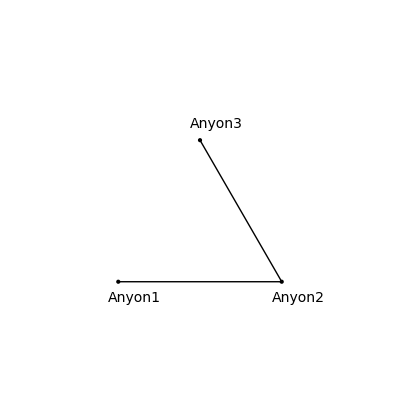

```mathematica
Graphics[visualizeAnyonStates[anyonPositions]]
```

```mathematica
braidStep1=PermutationProduct[Cycles[{{1,2}}],Cycles[{{2,3}}]];
newPositions=Part[anyonPositions,Permute[{1,2,3},braidStep1]];
```

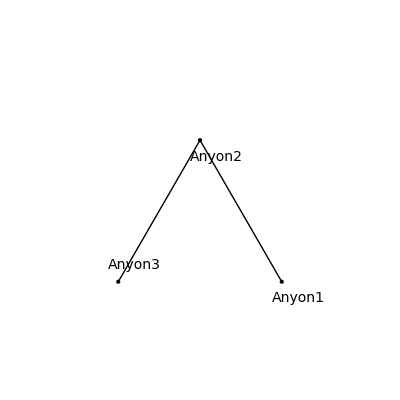

```mathematica
Graphics[visualizeAnyonStates[newPositions]]
```

```mathematica
(*Define braiding generators as quantum gates*)braidGenerator1={{0,1,0},{1,0,0},{0,0,1}};
braidGenerator2={{1,0,0},{0,0,1},{0,1,0}};
```

```mathematica
(*Apply braiding operations*)quantumGate1=MatrixPower[braidGenerator1,1];
quantumGate2=MatrixPower[braidGenerator2,1];
combinedGate=Dot[quantumGate1,quantumGate2];
MatrixForm[combinedGate]
```

(0 | 0 | 1
1 | 0 | 0
0 | 1 | 0)

```mathematica
(*Introduce random perturbations to simulate noise*)perturbationMatrix=RandomReal[{-0.01,0.01},{3,3}];
noisyGate=combinedGate+perturbationMatrix;
{MatrixForm[combinedGate],MatrixForm[noisyGate]}
```

{(0 | 0 | 1
1 | 0 | 0
0 | 1 | 0),(-0.00176625 | -0.00877914 | 0.991593
1.00938 | 0.000865099 | -0.00881753
-0.000875759 | 1.00898 | 0.00839383)}

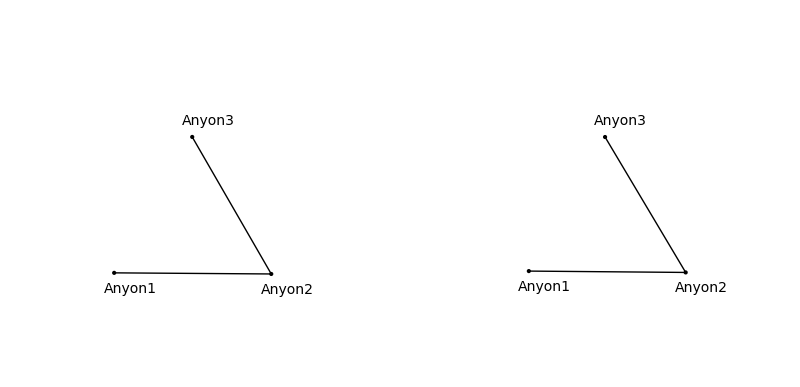

```mathematica
perturbedAnyonPositions=Map[anyonPositions+#&,perturbationMatrix];

anyonGraphics=Map[visualizeAnyonStates,perturbedAnyonPositions];
GraphicsGrid[Partition[anyonGraphics,2]]
```

```mathematica
(*Manipulate to control noise level with stronger perturbations*)Manipulate[(*Apply perturbations scaled by the noise level*)perturbedAnyonPositions=Map[anyonPositions+noiseLevel*#&,perturbationMatrix];
(*Create graphics for perturbed positions*)
anyonGraphics=Map[visualizeAnyonStates,perturbedAnyonPositions];
(*Display the grid of perturbed positions*)
GraphicsGrid[Partition[anyonGraphics,2]],
(*Control for the noise level*)
{{noiseLevel,0.5},0,2,0.05}]
```

```mathematica
(*Monte Carlo simulation for testing fault tolerance*)QuantumStateEvolution[initialState_,nSteps_]:=Module[{state=initialState},Do[state=Dot[state,braidGenerator1+RandomReal[{-0.01,0.01},{3,3}]];
state=Dot[state,braidGenerator2+RandomReal[{-0.01,0.01},{3,3}]],{nSteps}];
state];
```

```mathematica
finalState=QuantumStateEvolution[combinedGate,100];
MatrixForm[finalState]
```

(0.0480564 | 0.954013 | 0.00305212
-0.0406096 | -0.122406 | 0.931719
1.16457 | 0.0304322 | -0.0473103)

```mathematica
(*Error correction with noise amplitude and normalization*)QuantumStateWithErrorCorrection[initialState_,nSteps_,noiseAmplitude_]:=Module[{state=initialState},Do[(*Apply noisy braiding operations*)noisyBraid1=braidGenerator1+RandomReal[{-noiseAmplitude,noiseAmplitude},{3,3}];
noisyBraid2=braidGenerator2+RandomReal[{-noiseAmplitude,noiseAmplitude},{3,3}];
state=Dot[state,noisyBraid1];
state=Dot[state,noisyBraid2];
(*Normalize the state using Frobenius norm*)state=state/Norm[state,"Frobenius"],{nSteps}];
state];
```

```mathematica
correctedState=QuantumStateWithErrorCorrection[combinedGate,100,0.01];
MatrixForm[correctedState]
```

(0.013009 | 0.545499 | -0.0518766
0.011331 | -0.0836176 | 0.596631
0.571717 | 0.0339415 | 0.092026)